```mathematica
eq=D[u[x,t],t]+a*D[u[x,t],x]==0;
u0[x_]:=Sin[x]; 
(*a es la velocidad de propagación*)
a=1; 

solu=DSolve[{eq,u[x,0]==u0[x]},u[x,t],{x,t}];


Plot3D[Evaluate[u[x,t]/. solu],{x,0,4},{t,0,4},PlotRange->All,AxesLabel->{"x","t","u(x,t)"}]
```

-Graphics3D-

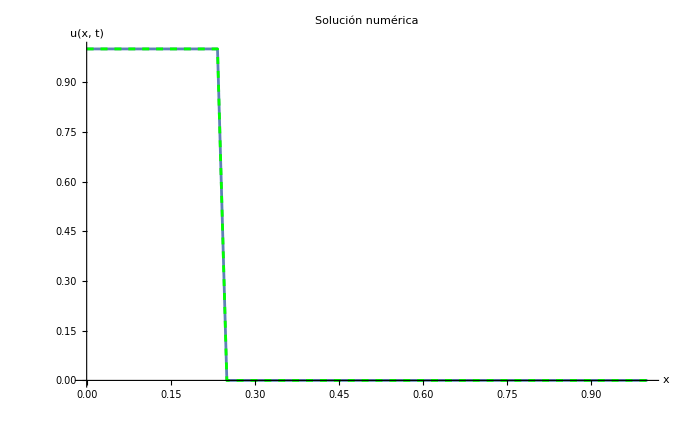

```mathematica
nx=60; 
dx=1/nx; 
tf=1/4;
dt=1/60; 
nt=tf/dt; 
a=1; 

(*Condicion inicial*)
σ=0.1; (*Ancho del pulso gaussiano*)

u0[x_]:=E^(-(x-0.5)^2/(2 σ^2));
u0[x_]:=Piecewise[{{1,x<0}},0];


Plot[u0[x],{x,-2,2},PlotRange->All];

(*Puntos*)
x=Table[(i*dx),{i,0,nx}];
t=Table[(n*dt),{n,0,nt}];

(*Solución exacta*)
uEx[x_,t_]:=u0[x-a*t];


uin=Table[uEx[0,t],{t,0,nt dt,dt}];

ut=ConstantArray[0,{nt+1,nx+1}];
ut[[1]]=Table[u0[x[[i]]],{i,1,Length[x]}];

(*Condiciones de contorno*)
ut[[All,1]]=uin;

(*Solución numérica*)
For[n=1,n<=nt,n++,
For[i=2,i<=nx,i++,
ut[[n+1,i]]=ut[[n,i]]-(a*dt/dx)*(ut[[n,i]]-ut[[n,i-1]]);
];
];
ut//MatrixForm;
solfinal=Table[{(i-1) dx,ut[[-1,i]]},{i,1,Length[ut[[-1]]]}];
solaprox=ListPlot[solfinal,Joined->True,PlotStyle->PointSize[Large],PlotRange->All,AxesLabel->{"x","u(x, t)"},PlotLabel->"Solución numérica"];

uExact=Table[{x,uEx[x,nt dt]},{x,0,1,dx}];
solexact=ListPlot[uExact,Joined->True,PlotStyle->{Dashed,Green},PlotStyle->PointSize[Large],PlotRange->All,AxesLabel->{"x","u(x, t)"},PlotLabel->"Solución exacta"];
Show[{solaprox,solexact},PlotRange->All]
```